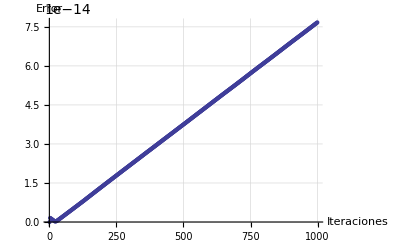

```mathematica
(* Horizontal test *)
SetOptions[{ListPlot, Plot},BaseStyle->{FontSize->14}];
ErrHorizontal = Import["/home/carlos/Documentos/Tesis/Codigo/QBill/Projects/Eclipse/Log/error_horizontal.csv"];

Show[
ListPlot[ErrHorizontal,
PlotRange->Full,
AxesOrigin->{0,0}, 
GridLines->Automatic,
AxesLabel->{"Iteraciones","Error"},
ImageSize->{550}
]
]
```

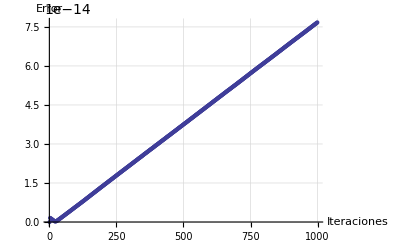

```mathematica
(* Vertical test *)
ErrVertical = Import["/home/carlos/Documentos/Tesis/Codigo/QBill/Projects/Eclipse/Log/error_vertical.csv"];
ListPlot[ErrVertical,
PlotRange->Full,
AxesOrigin->{0,0}, 
GridLines->Automatic,
AxesLabel->{"Iteraciones","Error"},
ImageSize->{550}
]
```

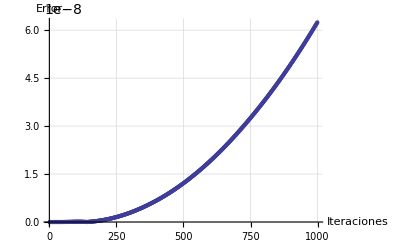

```mathematica
(* Diagonal ne test *)
ErrDiagonalNE= Import["/home/carlos/Documentos/Tesis/Codigo/QBill/Projects/Eclipse/Log/error_diag_ne.csv"];
ListPlot[ErrDiagonalNE,
PlotRange->Full,
AxesOrigin->{0,0}, 
GridLines->Automatic,
AxesLabel->{"Iteraciones","Error"},
ImageSize->{550}
]
```

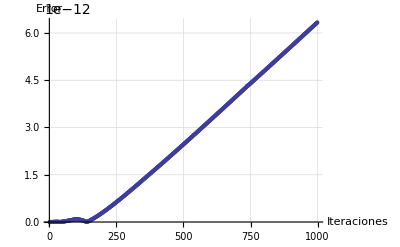

```mathematica
(* Diagonal se test *)
ErrDiagonalSE= Import["/home/carlos/Documentos/Tesis/Codigo/QBill/Projects/Eclipse/Log/error_diag_se.csv"];
ListPlot[ErrDiagonalSE,
PlotRange->Full,
AxesOrigin->{0,0}, 
GridLines->Automatic,
AxesLabel->{"Iteraciones","Error"},
ImageSize->{550}
]
```

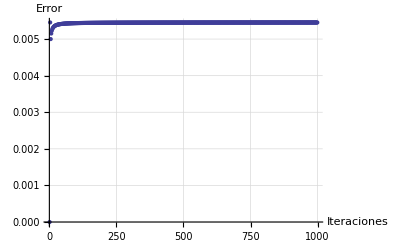

```mathematica
(* Linear test *)
ErrLineal= Import["/home/carlos/Documentos/Tesis/Codigo/QBill/Projects/Eclipse/Log/error_diag_l.csv"];
ListPlot[ErrLineal,
PlotRange->Full,
AxesOrigin->{0,0}, 
GridLines->Automatic,
AxesLabel->{"Iteraciones","Error"},
ImageSize->{550}
]
```

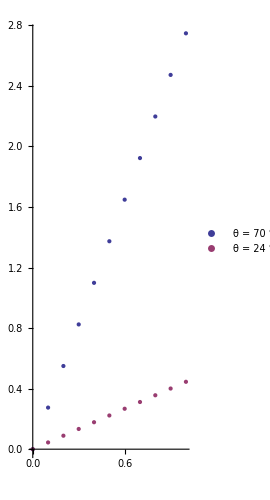

```mathematica
m1 = Tan[70 Degree];
m2 = Tan[24 Degree];
ListPlot[{Table[{x,m1 x},{x,0,1,0.1}],Table[{x,m2 x},{x,0,1,0.1}]}, 
AspectRatio->Automatic,
PlotStyle->PointSize[Medium],
PlotRange->Full,
AxesOrigin->{0,0},
PlotLegends->{"θ = 70 °","θ = 24 °"}
]
```

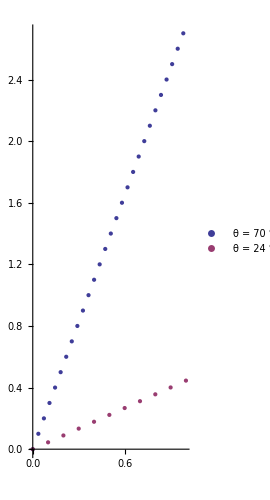

```mathematica
m1 = Tan[70 Degree];
m2 = Tan[24 Degree];
ListPlot[{Table[{y/m1,y},{y,0,m1,0.1}],Table[{x,m2 x},{x,0,1,0.1}]}, 
AspectRatio->Automatic,
PlotStyle->PointSize[Medium],
PlotRange->Full,
AxesOrigin->{0,0},
PlotLegends->{"θ = 70 °","θ = 24 °"},
PlotRange->All
]
```